```mathematica
ResourceFunction["EpicyclePlot"]
```

[◼] | EpicyclePlot

## 米奇

找一张图

```mathematica
Import["https://imgsa.baidu.com/exp/w=480/sign=a2113c06940a304e5222a1f2e1c8a7c3/5366d0160924ab18c825a93536fae6cd7b890b84.jpg"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageDimensions[-Graphics-]
```

{480,349}

裁掉多余的部分

```mathematica
ImageCrop[-Graphics-,{327,Full},Right]
```

-Graphics-

二值化提取边缘

```mathematica
Manipulate[Binarize[-Graphics-,t],{t,0,1}]
```

提取点

```mathematica
rawpts=PixelValuePositions[-Graphics-,0];
```

预览检验

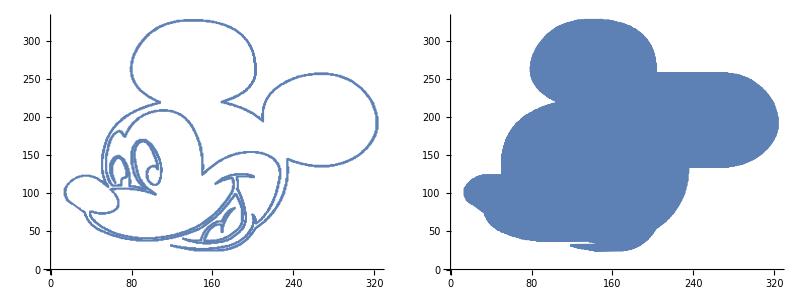

```mathematica
Grid@{{ListPlot[rawpts],ListLinePlot[rawpts]}}
```

显然点的顺序不对，用最短路找到正确的顺序

```mathematica
path=Last@FindShortestTour[rawpts];
path=path[[;;;;5]];
```

```mathematica
pts=rawpts[[path]];
```

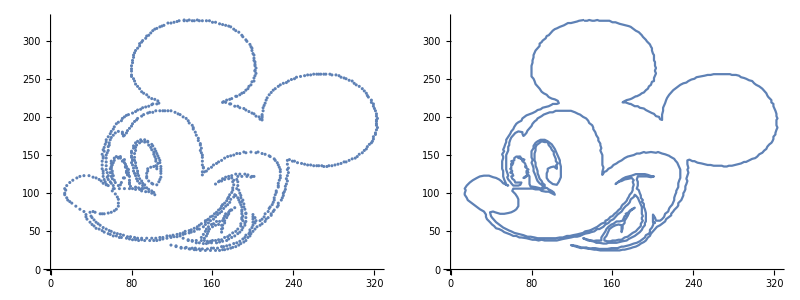

```mathematica
Grid@{{ListPlot[pts],ListLinePlot[pts]}}
```

```mathematica
z=pts[[All,1]]+I*pts[[All,2]];
```

```mathematica
ft=Chop[Fourier[z,FourierParameters->{0,-1}]];
```

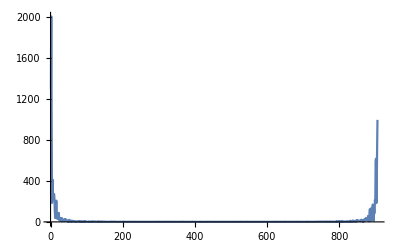

```mathematica
ListLinePlot[Abs@ft[[2;;]],PlotRange->All]
```

```mathematica
m=20;
pft=ft[[2;;Min[m,Quotient[Length[ft],2]]]];
nft=ft[[-1;;-Min[m,Quotient[Length[ft],2]];;-1]];
```

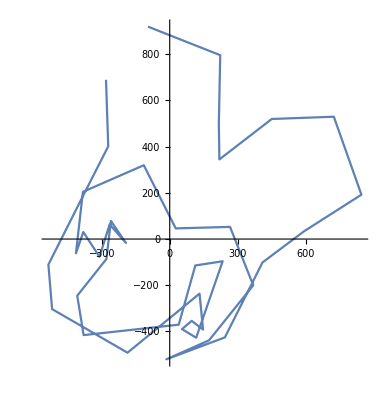

```mathematica
ComplexListPlot[InverseFourier[Join[{0},pft,Reverse@nft]],Joined->True]
```

```mathematica
fs=1;
epicycle=Join[Table[{Abs@pft[[i]],-i*fs,-Arg@pft[[i]]},{i,Length[pft]}],
Table[{Abs@nft[[i]],i*fs,-Arg@nft[[i]]},{i,Length[nft]}]
];
```

```mathematica
Rationalize[epicycle,0.01]//N//Compress//StringLength
```

854

```mathematica
Compress[epicycle]//StringLength
```

2726

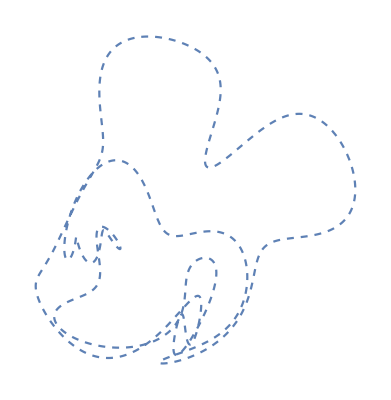

```mathematica
ResourceFunction["EpicyclePlot"][epicycle,1,{0,2π},"SpokeStyle"->None,"CircleStyle"->None,"PointStyle"->None]
```

## 松鼠

```mathematica
Import["https://timgsa.baidu.com/timg?image&quality=80&size=b9999_10000&sec=1579600894767&di=4c3c4acdf98318d29572375345ebd291&imgtype=0&src=http%3A%2F%2F5b0988e595225.cdn.sohucs.com%2Fimages%2F20180722%2F8f327a11fdbc4fbd851ef94f0b5f220a.jpeg"]
```

-Graphics-

```mathematica
img=Binarize[-Graphics-]//ImageCrop//ColorNegate//Thinning
```

-Graphics-

```mathematica
rawpts=PixelValuePositions[img,1];
```

预览检验

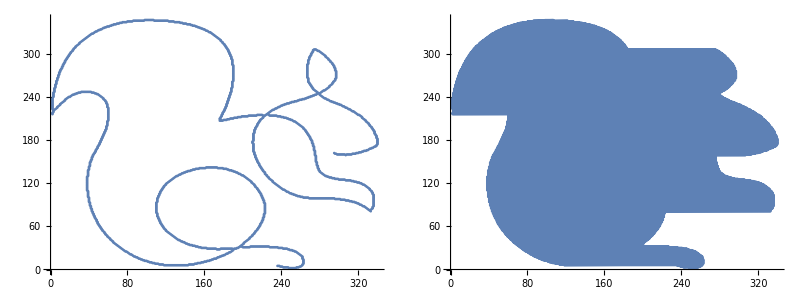

```mathematica
Grid@{{ListPlot[rawpts],ListLinePlot[rawpts]}}
```

显然点的顺序不对，要用最短路找到正确的顺序

```mathematica
Position[rawpts,{235,4}+1,{1}]
```

{{1871}}

```mathematica
Position[rawpts,{294,161}+1,{1}]
```

{{949}}

```mathematica
path=Last@FindShortestTour[rawpts,949,1871];
path=path[[;;;;5]];
```

```mathematica
pts=rawpts[[path]];
```

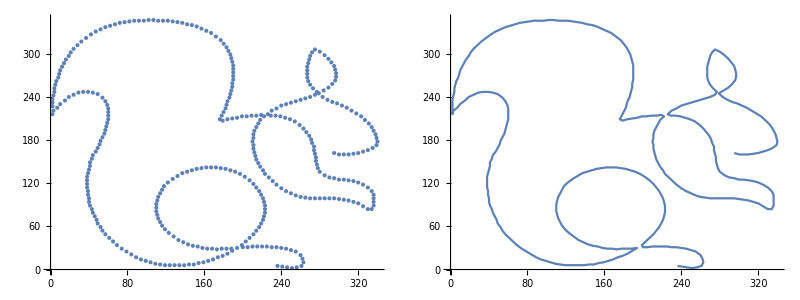

```mathematica
Grid@{{ListPlot[pts],ListLinePlot[pts]}}
```

看来还是不太对

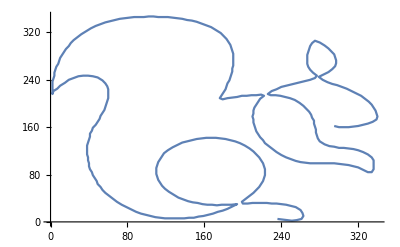

```mathematica
ListLinePlot[pts]
```

手动描一遍

```mathematica
DynamicModule[{tmp={}},
Column@{
EventHandler[Image[img,ImageSize->Full],"MouseDragged":>(tmp=DeleteDuplicates@Join[tmp,Nearest[pts,ImageDimensions[img]MousePosition["GraphicsImageScaled"],1]])],
Dynamic@ListLinePlot[tmp],
Row@{Button["OK",pts=tmp],Button["Reset",tmp={}]}
}
]
```

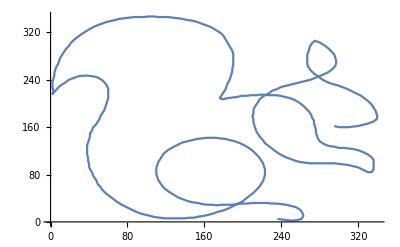

```mathematica
ListLinePlot[pts]
```

```mathematica
z=pts[[All,1]]+I*pts[[All,2]];
```

```mathematica
ft=Chop[Fourier[z,FourierParameters->{0,-1}]];
```

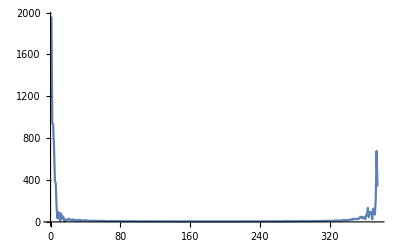

```mathematica
ListLinePlot[Abs@ft[[2;;]],PlotRange->All]
```

```mathematica
m=20;
pft=ft[[2;;Min[m,Quotient[Length[ft],2]]]];
nft=ft[[-1;;-Min[m,Quotient[Length[ft],2]];;-1]];
```

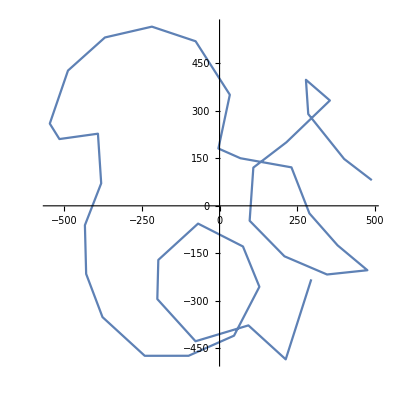

```mathematica
ComplexListPlot[InverseFourier[Join[{0},pft,Reverse@nft]],Joined->True]
```

```mathematica
fs=1;
epicycle=Join[Table[{Abs@pft[[i]],-i*fs,-Arg@pft[[i]]},{i,Length[pft]}],
Table[{Abs@nft[[i]],i*fs,-Arg@nft[[i]]},{i,Length[nft]}]
];
```

```mathematica
Compress[epicycle]//StringLength
```

1154

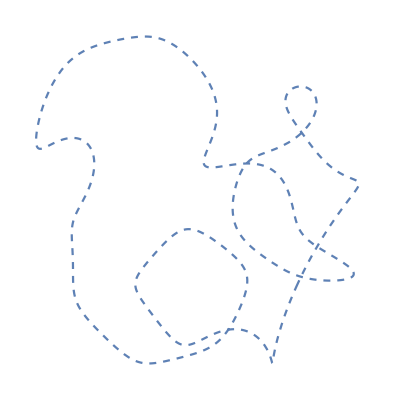

```mathematica
ResourceFunction["EpicyclePlot"][epicycle,1,{0,2π},"SpokeStyle"->None,"CircleStyle"->None,"PointStyle"->None]
```

## 皮卡丘

Pikachu curve

```mathematica
WolframAlpha["Pikachu curve",{{"EquationsPod:PopularCurveData",1},"ComputableData"}]
```

{Hold[x[t]==((-979/9-1/4 Sin[10/7-23 t]-3/10 Sin[4/3-22 t]-2/5 Sin[7/5-19 t]-1/5 Sin[7/5-16 t]-3/7 Sin[10/7-15 t]-3/8 Sin[13/9-9 t]-19/13 Sin[11/7-3 t]+222/5 Sin[11/7+t]+41/2 Sin[11/7+2 t]+34/9 Sin[11/7+4 t]+1/3 Sin[8/5+5 t]+3/8 Sin[8/5+6 t]+12/7 Sin[13/8+7 t]+11/7 Sin[13/8+8 t]+1/4 Sin[20/13+10 t]+2/9 Sin[16/9+11 t]+3/8 Sin[8/5+12 t]+1/3 Sin[7/4+13 t]+1/2 Sin[17/10+14 t]+5/7 Sin[17/10+17 t]+1/28 Sin[9/2+18 t]+1/2 Sin[12/7+20 t]+3/7 Sin[16/9+21 t]+6/11 Sin[7/4+24 t]) UnitStep[51 π-t] UnitStep[-47 π+t]+(-2765/8-6/5 Sin[14/9-22 t]-1/9 Sin[7/5-19 t]-9/8 Sin[14/9-18 t]-1/14 Sin[15/11-15 t]-6/5 Sin[11/7-12 t]-7/6 Sin[11/7-8 t]-29/10 Sin[11/7-6 t]-104/3 Sin[11/7-2 t]+415/18 Sin[11/7+t]+71/18 Sin[11/7+3 t]+19/8 Sin[33/7+4 t]+22/21 Sin[8/5+5 t]+3/8 Sin[61/13+7 t]+5/9 Sin[11/7+9 t]+1/8 Sin[14/3+10 t]+4/7 Sin[11/7+11 t]+4/11 Sin[14/3+13 t]+1/7 Sin[14/3+14 t]+2/7 Sin[5/3+16 t]+1/6 Sin[5/3+17 t]+6/7 Sin[8/5+20 t]+1/7 Sin[5/3+21 t]+1/6 Sin[8/5+23 t]) UnitStep[47 π-t] UnitStep[-43 π+t]+(-1627/7+1189/22 Sin[11/7+t]+3/4 Sin[13/8+2 t]+11/2 Sin[8/5+3 t]+2/7 Sin[17/7+4 t]+22/9 Sin[18/11+5 t]+1/4 Sin[17/7+6 t]+16/17 Sin[20/11+7 t]+1/5 Sin[29/9+8 t]) UnitStep[43 π-t] UnitStep[-39 π+t]+(-1190/9-3/7 Sin[1/18-5 t]-3/4 Sin[1/2-3 t]+109/9 Sin[13/10+t]+5/8 Sin[11/3+2 t]+5/9 Sin[10/3+4 t]+3/10 Sin[21/8+6 t]+2/9 Sin[2/3+7 t]+1/4 Sin[23/8+8 t]) UnitStep[39 π-t] UnitStep[-35 π+t]+(-369+188/21 Sin[27/28+t]+2/5 Sin[17/6+2 t]+2/3 Sin[91/23+3 t]+3/8 Sin[53/18+4 t]+2/11 Sin[1/7+5 t]) UnitStep[35 π-t] UnitStep[-31 π+t]+(-1915/8-8/9 Sin[1/10-12 t]-34/9 Sin[10/9-6 t]-137/10 Sin[5/7-2 t]+26/5 Sin[13/4+t]+118/5 Sin[11/8+3 t]+43/8 Sin[13/7+4 t]+49/6 Sin[11/12+5 t]+22/5 Sin[13/4+7 t]+17/16 Sin[1/7+8 t]+5/4 Sin[1/4+9 t]+5/7 Sin[17/5+10 t]+29/15 Sin[5/6+11 t]) UnitStep[31 π-t] UnitStep[-27 π+t]+(-2135/9-2/7 Sin[10/7-7 t]-Sin[1/27-4 t]+68/7 Sin[44/15+t]+76/9 Sin[37/10+2 t]+30/7 Sin[1+3 t]+8/9 Sin[3/2+5 t]+4/5 Sin[31/8+6 t]+3/7 Sin[10/3+8 t]+6/13 Sin[8/7+9 t]+1/3 Sin[31/9+10 t]) UnitStep[27 π-t] UnitStep[-23 π+t]+(1006/11-3/8 Sin[1/4-23 t]-3/5 Sin[1/8-22 t]-13/8 Sin[5/4-20 t]-9/7 Sin[3/2-16 t]-41/5 Sin[4/3-4 t]+768/7 Sin[11/5+t]+109/5 Sin[16/7+2 t]+150/13 Sin[11/6+3 t]+33/7 Sin[97/24+5 t]+23/4 Sin[5/7+6 t]+69/7 Sin[9/8+7 t]+32/5 Sin[21/5+8 t]+7/6 Sin[22/9+9 t]+28/5 Sin[5/6+10 t]+43/10 Sin[26/7+11 t]+14/9 Sin[5/11+12 t]+13/9 Sin[40/9+13 t]+11/6 Sin[2/5+14 t]+3/2 Sin[17/10+15 t]+7/11 Sin[4/3+17 t]+3/8 Sin[31/10+18 t]+4/7 Sin[14/9+19 t]+6/5 Sin[17/7+21 t]+4/7 Sin[27/8+24 t]) UnitStep[23 π-t] UnitStep[-19 π+t]+(-544/7-63/8 Sin[2/7-8 t]-38/13 Sin[11/9-6 t]-14/5 Sin[1/17-4 t]+77/9 Sin[1/2+t]+52/7 Sin[10/3+2 t]+22/9 Sin[76/17+3 t]+21/8 Sin[26/7+5 t]+3 Sin[15/8+7 t]+64/7 Sin[57/14+9 t]+6 Sin[17/6+10 t]) UnitStep[19 π-t] UnitStep[-15 π+t]+(-4406/11-37/10 Sin[4/7-5 t]-3 Sin[3/7-3 t]+24/7 Sin[7/6+t]+9/7 Sin[2/5+2 t]+31/15 Sin[37/8+4 t]+9/5 Sin[12/5+6 t]+59/12 Sin[13/6+7 t]+15/7 Sin[25/8+8 t]+134/15 Sin[7/3+9 t]+73/8 Sin[1/5+10 t]) UnitStep[15 π-t] UnitStep[-11 π+t]+(-627/5+236/7 Sin[6/5+t]+1/2 Sin[47/12+2 t]) UnitStep[11 π-t] UnitStep[-7 π+t]+(-715/2+69/2 Sin[5/6+t]) UnitStep[7 π-t] UnitStep[-3 π+t]+(-1891/8-19/9 Sin[6/5-21 t]-37/10 Sin[7/9-19 t]-23/8 Sin[1-17 t]-16/3 Sin[7/6-16 t]-29/5 Sin[1/5-9 t]-919/11 Sin[1/7-3 t]+1573/6 Sin[91/45+t]+214/5 Sin[33/8+2 t]+421/14 Sin[13/8+4 t]+61/6 Sin[19/5+5 t]+401/16 Sin[43/14+6 t]+511/51 Sin[35/8+7 t]+144/7 Sin[5/6+8 t]+137/10 Sin[25/13+10 t]+18/7 Sin[15/7+11 t]+17/9 Sin[41/9+12 t]+9/7 Sin[13/7+13 t]+29/10 Sin[22/7+14 t]+25/8 Sin[1/4+15 t]+12/5 Sin[11/8+18 t]+14/5 Sin[27/7+20 t]+13/8 Sin[12/7+22 t]+7/6 Sin[7/9+23 t]+26/11 Sin[23/7+24 t]) UnitStep[3 π-t] UnitStep[π+t]) UnitStep[√Sign[Sin[t/2]]]],Hold[y[t]==((-1538/7-8/11 Sin[11/8-22 t]-1/2 Sin[10/7-21 t]+67/6 Sin[33/7+t]+1478/29 Sin[11/7+2 t]+3/5 Sin[30/7+3 t]+26/3 Sin[11/7+4 t]+1/6 Sin[13/9+5 t]+30/29 Sin[8/5+6 t]+2/5 Sin[14/3+7 t]+88/29 Sin[8/5+8 t]+1/4 Sin[31/7+9 t]+11/8 Sin[8/5+10 t]+1/16 Sin[9/2+11 t]+1/12 Sin[5/4+12 t]+1/10 Sin[25/11+13 t]+11/8 Sin[18/11+14 t]+2/7 Sin[37/8+15 t]+1/6 Sin[11/8+16 t]+2/9 Sin[5/3+17 t]+1/5 Sin[17/10+18 t]+1/13 Sin[19/8+19 t]+23/24 Sin[12/7+20 t]+7/11 Sin[9/5+23 t]+9/7 Sin[7/4+24 t]) UnitStep[51 π-t] UnitStep[-47 π+t]+(-1867/8-2/7 Sin[20/13-23 t]-1/6 Sin[3/2-20 t]-5/7 Sin[20/13-17 t]-1/9 Sin[20/13-11 t]-1/6 Sin[13/9-9 t]-19/6 Sin[17/11-3 t]+263/5 Sin[11/7+t]+614/15 Sin[11/7+2 t]+87/10 Sin[11/7+4 t]+1/7 Sin[11/8+5 t]+19/11 Sin[11/7+6 t]+7/5 Sin[11/7+7 t]+4/3 Sin[8/5+8 t]+9/5 Sin[14/9+10 t]+4/7 Sin[8/5+12 t]+3/11 Sin[3/2+13 t]+1/8 Sin[22/15+14 t]+1/9 Sin[12/7+15 t]+6/5 Sin[11/7+16 t]+2/9 Sin[11/7+18 t]+3/5 Sin[8/5+19 t]+1/26 Sin[15/11+21 t]+6/7 Sin[8/5+22 t]) UnitStep[47 π-t] UnitStep[-43 π+t]+(-143/10+118/39 Sin[11/7+t]+40/7 Sin[33/7+2 t]+49/25 Sin[14/3+3 t]+12/5 Sin[8/5+4 t]+1/9 Sin[32/13+5 t]+5/2 Sin[13/8+6 t]+2/5 Sin[22/5+7 t]+3/4 Sin[7/4+8 t]) UnitStep[43 π-t] UnitStep[-39 π+t]+(665/6-1/8 Sin[2/3-8 t]-1/2 Sin[7/5-2 t]-246/19 Sin[1/7-t]+1/4 Sin[33/16+3 t]+1/6 Sin[17/6+4 t]+1/5 Sin[31/7+5 t]+1/11 Sin[50/17+6 t]+1/8 Sin[30/7+7 t]) UnitStep[39 π-t] UnitStep[-35 π+t]+(1023/10-119/10 Sin[7/15-t]+2/11 Sin[25/7+2 t]+2/9 Sin[5/8+3 t]+1/5 Sin[33/7+4 t]+1/4 Sin[19/10+5 t]) UnitStep[35 π-t] UnitStep[-31 π+t]+(-862/7-1/7 Sin[2/7-12 t]-1/8 Sin[3/10-5 t]+25/7 Sin[77/17+t]+355/59 Sin[41/40+2 t]+27/5 Sin[46/15+3 t]+33/7 Sin[11/3+4 t]+27/10 Sin[13/9+6 t]+5/11 Sin[11/5+7 t]+5/8 Sin[3+8 t]+8/5 Sin[16/15+9 t]+16/15 Sin[1/7+10 t]+7/9 Sin[12/5+11 t]) UnitStep[31 π-t] UnitStep[-27 π+t]+(201/5-1/3 Sin[5/4-8 t]-2/5 Sin[5/9-7 t]-5/7 Sin[11/8-5 t]-7/2 Sin[15/14-2 t]+29/8 Sin[41/10+t]+11/6 Sin[13/3+3 t]+7/6 Sin[1/27+4 t]+2/7 Sin[8/7+6 t]+1/9 Sin[9/5+9 t]+2/7 Sin[1/10+10 t]) UnitStep[27 π-t] UnitStep[-23 π+t]+(-243/8-4/11 Sin[8/9-12 t]-10/7 Sin[19/13-10 t]+623/3 Sin[10/7+t]+39/5 Sin[10/11+2 t]+251/9 Sin[4/3+3 t]+5/7 Sin[4/3+4 t]+61/6 Sin[4/3+5 t]+14/9 Sin[23/7+6 t]+76/25 Sin[9/7+7 t]+3/4 Sin[1/4+8 t]+19/5 Sin[3/2+9 t]+17/6 Sin[6/5+11 t]+13/8 Sin[14/13+13 t]+8/9 Sin[17/6+14 t]+24/25 Sin[1/2+15 t]+1/6 Sin[13/8+16 t]+5/8 Sin[1+17 t]+1/7 Sin[18/17+18 t]+6/7 Sin[1+19 t]+1/4 Sin[4/9+20 t]+2/7 Sin[7/5+21 t]+1/3 Sin[8/7+22 t]+2/5 Sin[1/26+23 t]+2/11 Sin[8/7+24 t]) UnitStep[23 π-t] UnitStep[-19 π+t]+(27/5-111/10 Sin[4/5-9 t]-12/5 Sin[7/13-2 t]+1/6 Sin[48/11+t]+13/8 Sin[27/7+3 t]+71/24 Sin[6/11+4 t]+22/9 Sin[7/2+5 t]+19/7 Sin[8/17+6 t]+20/7 Sin[34/9+7 t]+55/7 Sin[6/5+8 t]+64/9 Sin[38/9+10 t]) UnitStep[19 π-t] UnitStep[-15 π+t]+(-27/2-22/7 Sin[4/3-8 t]-19/7 Sin[20/13-6 t]+38/13 Sin[1/24+t]+12/11 Sin[5/9+2 t]+26/7 Sin[7/9+3 t]+11/5 Sin[12/11+4 t]+37/10 Sin[17/10+5 t]+51/10 Sin[10/3+7 t]+33/4 Sin[26/7+9 t]+41/5 Sin[9/5+10 t]) UnitStep[15 π-t] UnitStep[-11 π+t]+(2303/24-172/5 Sin[3/8-t]+5/4 Sin[7/2+2 t]) UnitStep[11 π-t] UnitStep[-7 π+t]+(441/5-455/12 Sin[7/9-t]) UnitStep[7 π-t] UnitStep[-3 π+t]+(-211/5-1/3 Sin[1/20-18 t]-7/5 Sin[7/9-17 t]-18/11 Sin[2/5-14 t]-24/5 Sin[1/13-9 t]+2767/7 Sin[11/3+t]+229/5 Sin[17/7+2 t]+313/8 Sin[22/5+3 t]+32/3 Sin[22/5+4 t]+169/6 Sin[21/8+5 t]+23/7 Sin[26/11+6 t]+21/2 Sin[5/6+7 t]+55/6 Sin[14/5+8 t]+212/13 Sin[24/7+10 t]+26/9 Sin[9/2+11 t]+16/5 Sin[25/6+12 t]+35/17 Sin[4/11+13 t]+15/8 Sin[7/10+15 t]+2/3 Sin[20/9+16 t]+16/7 Sin[4/5+19 t]+13/7 Sin[29/7+20 t]+14/3 Sin[7/5+21 t]+4/3 Sin[7/4+22 t]+12/7 Sin[34/33+23 t]+7/4 Sin[27/7+24 t]) UnitStep[3 π-t] UnitStep[π+t]) UnitStep[√Sign[Sin[t/2]]]]}

```mathematica
img=Binarize[-Graphics-]//ImageCrop//ColorNegate//Thinning
```

-Graphics-

```mathematica
rawpts=PixelValuePositions[img,1];
```

预览检验

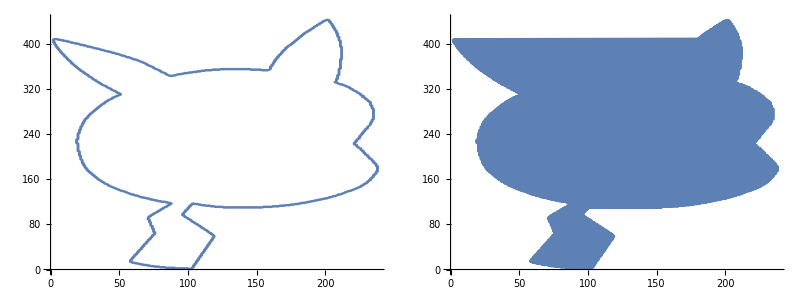

```mathematica
Grid@{{ListPlot[rawpts],ListLinePlot[rawpts]}}
```

显然点的顺序不对，要用最短路找到正确的顺序

```mathematica
path=Last@FindShortestTour[rawpts];
path=path[[;;;;5]];
```

```mathematica
pts=rawpts[[path]];
```

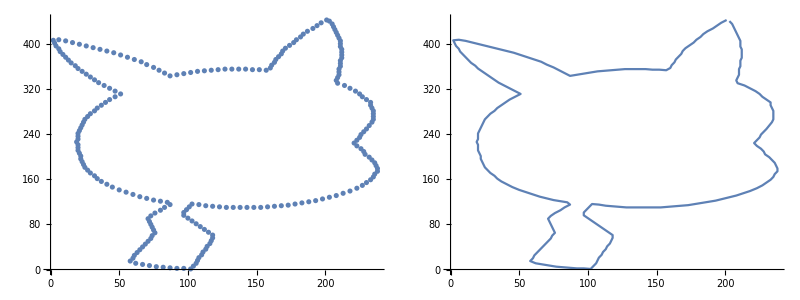

```mathematica
Grid@{{ListPlot[pts],ListLinePlot[pts]}}
```

```mathematica
z=pts[[All,1]]+I*pts[[All,2]];
```

```mathematica
ft=Chop[Fourier[z,FourierParameters->{0,-1}]];
```

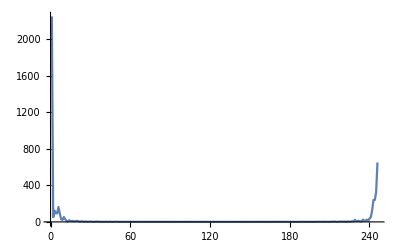

```mathematica
ListLinePlot[Abs@ft[[2;;]],PlotRange->All]
```

```mathematica
m=10;
pft=ft[[2;;Min[m,Quotient[Length[ft],2]]]];
nft=ft[[-1;;-Min[m,Quotient[Length[ft],2]];;-1]];
```

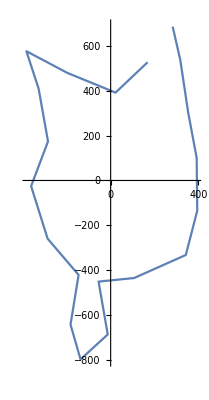

```mathematica
ComplexListPlot[InverseFourier[Join[{0},pft,Reverse@nft]],Joined->True]
```

```mathematica
fs=1;
epicycle=Join[Table[{Abs@pft[[i]],-i*fs,-Arg@pft[[i]]},{i,Length[pft]}],
Table[{Abs@nft[[i]],i*fs,-Arg@nft[[i]]},{i,Length[nft]}]
];
```

```mathematica
epicycle//TextString//StringLength
```

974

```mathematica
SetPrecision[epicycle,2]//TextString//StringLength
```

359

```mathematica
Compress[epicycle]//StringLength
```

1154

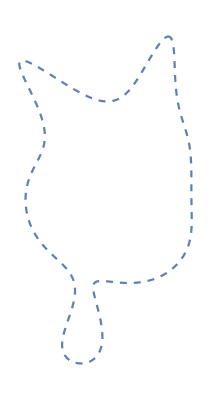

```mathematica
ResourceFunction["EpicyclePlot"][SetPrecision[epicycle,2],1,{0,2π},"SpokeStyle"->None,"CircleStyle"->None,"PointStyle"->None]
```